(*Example of calculating ioninc conductivity using FOH and MD simulated parameters for LiPF6 in EC DMC in a large concentration range*)

(*This script is to calculate the conductance using the theory presented by Fernandex-Prini-Spiro1973 book with book name conductance and transference number*)

```mathematica
(*-------------------Constants for use for the specific example---------------------*)
epslon = 31.41 ;(* from EXP, measured, EC/DMC data from Naejus, R., Lemordant, D. J.Chem. Thermodynamics 29 1997*)
viscosity = 1.21*0.01; (* in the unit of poise, EC/DMC data from Berhaut*)
T = 298;(* condition *)

alpha = 82.0460*10^4/(epslon * T)^1.5; (*Debye Huckel limiting law*)

beta = 82.487 / (viscosity*(epslon * T)^0.5); (*Debye Huckel limiting law*)

E1 = 2.94257 * 10^12 / (epslon * T)^3*2.29; (*Debye Huckel limiting law*)

E2 = 4.33244 * 10^7 / ((epslon * T)^2*viscosity)*2.29;(*Debye Huckel limiting law*)
(* --------------------------------coefficients for model--------------------------- *)
aMD = 4.3;
condnodMD = 34.4(*best fit 32.15, higher bound 34.4, lower bound 30.26*);
ratio = 0.5; (*mass balance for salt dissociation to ions*)
SMD = alpha * condnodMD+ beta;
EcoeffMD = E1 * condnodMD - E2;
(* alpha, beta, E1, E2 should not change since they are dependent on solvent base *)
(* assuming super dilute conductivity does not change as well, then S, and Ecoeff do not change *)
(* kappa coefficient part won't change *)
ba = 16.7009 * 10^4 /(epslon * T); (* unit Angstrom *)
kap = 50.2916/(epslon * T)^0.5 ; (*kappa term*)
kapaMD = aMD*kap; (*kappa term times parameter a obtained from MD RDF analyses*)
kapba = ba * kap; (*kappa times b term and a parameter*)
bMD = ba / aMD;(*calculate the b term from a*)
```

```mathematica
(*--------------------MD simulated SSIP fraction-----------------------------*)
SSIP = {0.9692, 0.9306, 0.9327,0.9213,0.9019, 0.8904, 0.8454,0.8221, 0.7947, 0.7583,0.65,0.575}*ratio;
(*the fraction of SSIP obtained from solvation cluster types and densities analysis*)
concMD = {0.14, 0.26,0.33,0.37, 0.44, 0.58, 0.9,1.05, 1.25, 1.55,1.99,2.28};
(*The concentration of LiPF6 sampled in the study*)
KAMDl = {};
lenMD = Length[SSIP];
For[i=1,i<(lenMD+1),i++,     
KAMD = (1-SSIP[[i]])*concMD[[i]]/((SSIP[[i]]*concMD[[i]])^2);
     AppendTo[KAMDl, KAMD]];
```

```mathematica
gammaconcmdl={};
For[i=1,i<(lenMD+1),i++,     
gammaconcmd = SSIP[[i]]*concMD[[i]];
     AppendTo[gammaconcmdl, gammaconcmd]];
```

```mathematica
delta1MD = 1/bMD^3*(2*bMD^2+2*bMD-1)+0.9073;
delta2MD = 22/(3*bMD)+0.0142;
delta3MD = 0.9571/bMD^3 + 1.1187/bMD^2 + 0.1523/bMD;
delta4MD = 1/bMD^3*(0.5738*bMD^2+7.0572*bMD - 2/3)-0.6461;
delta5MD = E2*beta/condnodMD * (4/(3*bMD)-2.2194);
```

```mathematica
(*---------------------J1 and J2 terms ---------------------------------------*)
J1MD = 2*E1 * condnodMD *(Log10[kapaMD]+delta1MD)+2*E2*(delta2MD-Log10[kapaMD]);
J2MD = kapba*(4*E1*condnodMD*delta3MD + 2*E2*delta4MD)-delta5MD ;
```

```mathematica
(*---------------------J terms for the conductance-----------------------------*)
JMDl = {};

For[i=1,i<(lenMD+1),i++,     JMD =J1MD * gammaconcmdl[[i]]-J2MD*(gammaconcmdl[[i]])^(3/2);
AppendTo[JMDl, JMD]
]
```

```mathematica
(* ------------------calculate the activity coefficients-----------------------*)
activitycoeffmdlist = {};
For[i=1,i<(lenMD+1),i++, 
activitycoeffmd =Exp[ kapba*(gammaconcmdl[[i]])^0.5/(2*(1+kapaMD*(gammaconcmdl[[i]])^0.5))];
AppendTo[activitycoeffmdlist,activitycoeffmd ]];
```

```mathematica
(*-----------------------start calculating conductance------------------------*)
conductanceMDlist={};
For[i=1,i<(lenMD+1),i++,     
result=Solve[ condnodMD- SMD*gammaconcmdl[[i]]^(1/2)+EcoeffMD *gammaconcmdl[[i]]*Log10[gammaconcmdl[[i]]]+JMDl[[i]]-KAMDl[[i]]*CDTMD*(activitycoeffmdlist[[i]])^2*gammaconcmdl[[i]]==0,CDTMD, Reals];
AppendTo[conductanceMDlist,result];
]

conductanceMDlist = 2*{CDTMD}/.conductanceMDlist;
```

```mathematica
(* ------------------calculate the ionic conductivity -------------------------*)
ioncondmdlist = {};
For[i=1,i<(lenMD+1),i++,     
ioncondmd =concMD[[i]]*conductanceMDlist[[i]];
AppendTo[ioncondmdlist, ioncondmd];
];
Print[ioncondmdlist]
```

{{{3.27467}},{{5.75819}},{{7.36264}},{{8.05126}},{{9.12691}},{{11.304}},{{13.6286}},{{13.6777}},{{12.9786}},{{10.5065}},{{7.44433}},{{6.67642}}}

{3.27467,5.75819,7.36264,8.05126,9.12691,11.304,13.6286,13.6777,12.9786,10.5065,7.44433,6.67642}

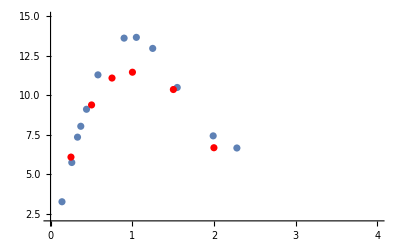

```mathematica
(* ---------------------------plot and show ------------------------------------*)
concMD=Flatten[concMD];
ioncondmdlist=Flatten[ioncondmdlist];
Print[ioncondmdlist]
(*experimental measurements from Berhaut et al. RSC.Adv, VOl 9, 2019 See manuscript *)
expcond = Flatten[{6.101,9.401,11.103,11.472,10.377,6.693}];
expconc = Flatten[{0.25,0.502,0.752,1.002,1.503,1.999}];

p1 = ListPlot[{Inner[List, concMD, ioncondmdlist, List]}, PlotRange->{{0,4},{2,15}}];
p2 = ListPlot[{Inner[List, expconc, expcond, List]}, PlotStyle->Red];
Show[p1, p2]
```